We have a boundary layer at x=1, and a corner layer at x=1/4. In order to determine the leading order uniform approximation, one needs to study the outer solution around x=0, with no perturbed terms, and then study the two layers

```mathematica
Clear[y,s,x]
```

```mathematica
s=NDSolve[{0.002*y''[x]-(x-0.25)*(x-0.75)*y'[x]-x*(y[x]-1)==0,y[0]==-2,y[1]==2},y,{x,0,1}](*Shooting Method for the exact soultion*)
```

{{y→InterpolatingFunction[…]}}

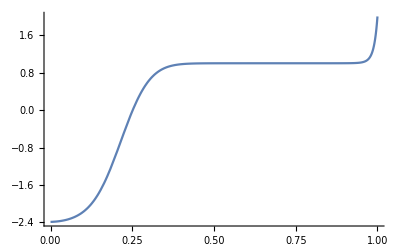

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

```mathematica
DSolve[{(-x^2+x-3/16)*y'[x]-x*(y[x]-1)==0,y[0]==-2},y[x],x]
```

{{y[x]→(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}

```mathematica
(-x^2+x-3/16)*D[1+Exp[3*(x-1)/(16*0.01)]]-x*(1+Exp[3*(x-1)/(16*0.01)])+x
```

x-(1+ⅇ^(18.75 (-1+x))) x+(1+ⅇ^(18.75 (-1+x))) (-3/16+x-x^2)

```mathematica
DSolve[{y''[x]-3*y'[x]/16==0},y[x],x]
```

{{y[x]→16/3 ⅇ^(3 x/16) C[1]+C[2]}}

```mathematica
{{y[x]->(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}(*Second boundary condition*)
```

{{y[x]→(-√3 √(1-4 x)+3 (3-4 x)^(3/2))/(3 (3-4 x)^(3/2))}}

```mathematica
{{y[x]->(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}(*First boundary condition*)
```

{{y[x]→(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2)}}

```mathematica
{{y[x]->ⅇ^(3 x/16) +1}}(*Boundary layer at x=1*)
```

{{y[x]→1+ⅇ^(3 x/16)}}

```mathematica
Table[1+Exp[3*(x-1)/(16*0.01)],{x,1/4,1,0.05}]
```

{1.,1.,1.00001,1.00001,1.00003,1.00008,1.00022,1.00055,1.00141,1.00361,1.00921,1.02352,1.06005,1.15335,1.39161,2.}

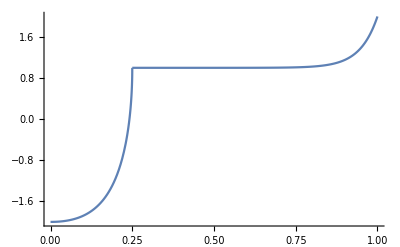

```mathematica
Show[Plot[1+Exp[3*(x-1)/(16*0.01)],{x,1/4,1},PlotRange->All],Plot[(-9 √3 √(1-4 x)+(3-4 x)^(3/2))/(3-4 x)^(3/2),{x,0,1/4},PlotRange->All]]
```

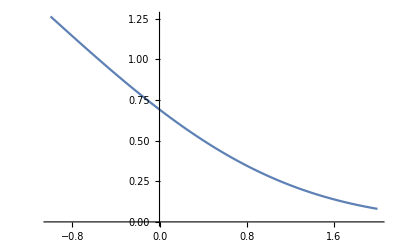

```mathematica
Plot[ⅇ^(-x^2/4)  HermiteH[-3/2,x/2],{x,-1,2}]
```

```mathematica
(*Corner layer*)
```

When studying the corner layer around x=1/4, we need to rescale such that Tϵ^1/2=x-1/4

```mathematica
DSolve[{z''[x]+(x*z'[x]/2)-((z[x])/4)==0},z[x],x]
```

{{z[x]→ⅇ^(-x^2/4) C[1] HermiteH[-3/2,x/2]+ⅇ^(-x^2/4) C[2] Hypergeometric1F1[3/4,1/2,x^2/4]}}

```mathematica
AsymptoticDSolveValue[{z''[x]+(x*z'[x]/2)-((z[x])/4)==0},z[x],{x,-Infinity,5}]
```

(-315/(128 (-x)^(11/2))-15/(32 (-x)^(7/2))-1/(4 (-x)^(3/2))+√-x) C[1]+ⅇ^(-x^2/4) (-45045/(128 (-x)^(15/2))+945/(32 (-x)^(11/2))-15/(4 (-x)^(7/2))+1/(-x)^(3/2)) C[2]

```mathematica
{{z[x]->1+ⅇ^(-x^2/4) C[1] HermiteH[-3/2,x/2]+ⅇ^(-x^2/4) C[2] Hypergeometric1F1[3/4,1/2,x^2/4]}}(*Corner layer*)
```

{{z[x]→1+ⅇ^(-x^2/4) C[1] HermiteH[-3/2,x/2]+ⅇ^(-x^2/4) C[2] Hypergeometric1F1[3/4,1/2,x^2/4]}}